```mathematica
LinearAlgebra
```

LinearAlgebra

```mathematica
<<.b4LinearAlgebra
```

Get::noopen: Cannot open .b4LinearAlgebra.

$Failed

```mathematica
Vandermonde[a_List?VectorQ]:=Outer[Power,a,Range[Length[a]]-1]
```

```mathematica
validPartitionQ[part_]:=VectorQ[part,(IntegerQ[#]&&NonNegative[#])&]&&Apply[GreaterEqual,part]

SchurPolynomial[part_?validPartitionQ,vars_List]/;Length[part]≤Length[vars]:=Module[{n=Length[vars],tmp},tmp=Table[Indexed[C,i],{i,Range[n]}];
Cancel[Det[Outer[Power,tmp,PadLeft[Reverse[part],n]+Range[0,n-1]]]/Det[Vandermonde[tmp]]]/.Thread[tmp:>vars]]

MonomialSymmetricPolynomial[part_?validPartitionQ,vars_List]/;Length[part]≤Length[vars]:=Module[{n=Length[vars],tmp},tmp=C/@Range[n];
Sum[Inner[Power,tmp,perm,Times],{perm,Permutations[PadRight[part,n]]}]/.Thread[tmp:>vars]]

reverseLexicographicQ[p1_?validPartitionQ,p2_?validPartitionQ]/;Total[p1]==Total[p2]:=p1===p2||Catch[Scan[With[{tmp=Order@@#},If[tmp≠0,Throw[tmp==-1]]]&,Flatten[{p1,p2},{{2},{1}}]]]

KostkaNumber[p1_,p1_]/;validPartitionQ[p1]:=1

KostkaNumber[{n_Integer},p2_?validPartitionQ]/;Total[p2]==n:=1

KostkaNumber[p1_?validPartitionQ,p2_?validPartitionQ]/;Total[p1]==Total[p2]&&!reverseLexicographicQ[p1,p2]:=0

KostkaNumber[p1_?validPartitionQ,p2_?validPartitionQ]/;Total[p1]==Total[p2]:=KostkaNumber[p1,p2]=Module[{n=Total[p1],m,pl,tmp},m=Max[Length[p1],Length[p2]];tmp=C/@Range[m];pl=IntegerPartitions[n,m];
Extract[First[PolynomialReduce[SchurPolynomial[p1,tmp],Table[MonomialSymmetricPolynomial[ip,tmp],{ip,pl}],tmp,CoefficientDomain->Integers,MonomialOrder->Lexicographic]],First[Position[pl,p2]]]]
```

```mathematica
SchurPolynomial[First[IntegerPartitions[4,3]],{x,y,z}]
```

x^4+x^3 y+x^2 y^2+x y^3+y^4+x^3 z+x^2 y z+x y^2 z+y^3 z+x^2 z^2+x y z^2+y^2 z^2+x z^3+y z^3+z^4

```mathematica
Table[
Factor[SchurPolynomial[#,Table[Indexed[x,i],{i,max}]]]&/@PadRight[IntegerPartitions[5,max]]//MatrixForm,
{max,1,5}
]//Column
```

(x1^5)
((x1+x2) (x1^2-x1 x2+x2^2) (x1^2+x1 x2+x2^2)
x1 x2 (x1+x2) (x1^2+x2^2)
x1^2 x2^2 (x1+x2))
(x1^5+x1^4 x2+x1^3 x2^2+x1^2 x2^3+x1 x2^4+x2^5+x1^4 x3+x1^3 x2 x3+x1^2 x2^2 x3+x1 x2^3 x3+x2^4 x3+x1^3 x3^2+x1^2 x2 x3^2+x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3+x1 x3^4+x2 x3^4+x3^5
(x1+x2) (x1+x3) (x2+x3) (x1^2+x2^2+x3^2)
x1^3 x2^2+x1^2 x2^3+x1^3 x2 x3+2 x1^2 x2^2 x3+x1 x2^3 x3+x1^3 x3^2+2 x1^2 x2 x3^2+2 x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3
x1 x2 x3 (x1^2+x1 x2+x2^2+x1 x3+x2 x3+x3^2)
x1 x2 x3 (x1 x2+x1 x3+x2 x3))
(x1^5+x1^4 x2+x1^3 x2^2+x1^2 x2^3+x1 x2^4+x2^5+x1^4 x3+x1^3 x2 x3+x1^2 x2^2 x3+x1 x2^3 x3+x2^4 x3+x1^3 x3^2+x1^2 x2 x3^2+x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3+x1 x3^4+x2 x3^4+x3^5+x1^4 x4+x1^3 x2 x4+x1^2 x2^2 x4+x1 x2^3 x4+x2^4 x4+x1^3 x3 x4+x1^2 x2 x3 x4+x1 x2^2 x3 x4+x2^3 x3 x4+x1^2 x3^2 x4+x1 x2 x3^2 x4+x2^2 x3^2 x4+x1 x3^3 x4+x2 x3^3 x4+x3^4 x4+x1^3 x4^2+x1^2 x2 x4^2+x1 x2^2 x4^2+x2^3 x4^2+x1^2 x3 x4^2+x1 x2 x3 x4^2+x2^2 x3 x4^2+x1 x3^2 x4^2+x2 x3^2 x4^2+x3^3 x4^2+x1^2 x4^3+x1 x2 x4^3+x2^2 x4^3+x1 x3 x4^3+x2 x3 x4^3+x3^2 x4^3+x1 x4^4+x2 x4^4+x3 x4^4+x4^5
x1^4 x2+x1^3 x2^2+x1^2 x2^3+x1 x2^4+x1^4 x3+2 x1^3 x2 x3+2 x1^2 x2^2 x3+2 x1 x2^3 x3+x2^4 x3+x1^3 x3^2+2 x1^2 x2 x3^2+2 x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+2 x1 x2 x3^3+x2^2 x3^3+x1 x3^4+x2 x3^4+x1^4 x4+2 x1^3 x2 x4+2 x1^2 x2^2 x4+2 x1 x2^3 x4+x2^4 x4+2 x1^3 x3 x4+3 x1^2 x2 x3 x4+3 x1 x2^2 x3 x4+2 x2^3 x3 x4+2 x1^2 x3^2 x4+3 x1 x2 x3^2 x4+2 x2^2 x3^2 x4+2 x1 x3^3 x4+2 x2 x3^3 x4+x3^4 x4+x1^3 x4^2+2 x1^2 x2 x4^2+2 x1 x2^2 x4^2+x2^3 x4^2+2 x1^2 x3 x4^2+3 x1 x2 x3 x4^2+2 x2^2 x3 x4^2+2 x1 x3^2 x4^2+2 x2 x3^2 x4^2+x3^3 x4^2+x1^2 x4^3+2 x1 x2 x4^3+x2^2 x4^3+2 x1 x3 x4^3+2 x2 x3 x4^3+x3^2 x4^3+x1 x4^4+x2 x4^4+x3 x4^4
x1^3 x2^2+x1^2 x2^3+x1^3 x2 x3+2 x1^2 x2^2 x3+x1 x2^3 x3+x1^3 x3^2+2 x1^2 x2 x3^2+2 x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3+x1^3 x2 x4+2 x1^2 x2^2 x4+x1 x2^3 x4+x1^3 x3 x4+3 x1^2 x2 x3 x4+3 x1 x2^2 x3 x4+x2^3 x3 x4+2 x1^2 x3^2 x4+3 x1 x2 x3^2 x4+2 x2^2 x3^2 x4+x1 x3^3 x4+x2 x3^3 x4+x1^3 x4^2+2 x1^2 x2 x4^2+2 x1 x2^2 x4^2+x2^3 x4^2+2 x1^2 x3 x4^2+3 x1 x2 x3 x4^2+2 x2^2 x3 x4^2+2 x1 x3^2 x4^2+2 x2 x3^2 x4^2+x3^3 x4^2+x1^2 x4^3+x1 x2 x4^3+x2^2 x4^3+x1 x3 x4^3+x2 x3 x4^3+x3^2 x4^3
x1^3 x2 x3+x1^2 x2^2 x3+x1 x2^3 x3+x1^2 x2 x3^2+x1 x2^2 x3^2+x1 x2 x3^3+x1^3 x2 x4+x1^2 x2^2 x4+x1 x2^3 x4+x1^3 x3 x4+3 x1^2 x2 x3 x4+3 x1 x2^2 x3 x4+x2^3 x3 x4+x1^2 x3^2 x4+3 x1 x2 x3^2 x4+x2^2 x3^2 x4+x1 x3^3 x4+x2 x3^3 x4+x1^2 x2 x4^2+x1 x2^2 x4^2+x1^2 x3 x4^2+3 x1 x2 x3 x4^2+x2^2 x3 x4^2+x1 x3^2 x4^2+x2 x3^2 x4^2+x1 x2 x4^3+x1 x3 x4^3+x2 x3 x4^3
x1^2 x2^2 x3+x1^2 x2 x3^2+x1 x2^2 x3^2+x1^2 x2^2 x4+2 x1^2 x2 x3 x4+2 x1 x2^2 x3 x4+x1^2 x3^2 x4+2 x1 x2 x3^2 x4+x2^2 x3^2 x4+x1^2 x2 x4^2+x1 x2^2 x4^2+x1^2 x3 x4^2+2 x1 x2 x3 x4^2+x2^2 x3 x4^2+x1 x3^2 x4^2+x2 x3^2 x4^2
x1 x2 x3 x4 (x1+x2+x3+x4))
(x1^5+x1^4 x2+x1^3 x2^2+x1^2 x2^3+x1 x2^4+x2^5+x1^4 x3+x1^3 x2 x3+x1^2 x2^2 x3+x1 x2^3 x3+x2^4 x3+x1^3 x3^2+x1^2 x2 x3^2+x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3+x1 x3^4+x2 x3^4+x3^5+x1^4 x4+x1^3 x2 x4+x1^2 x2^2 x4+x1 x2^3 x4+x2^4 x4+x1^3 x3 x4+x1^2 x2 x3 x4+x1 x2^2 x3 x4+x2^3 x3 x4+x1^2 x3^2 x4+x1 x2 x3^2 x4+x2^2 x3^2 x4+x1 x3^3 x4+x2 x3^3 x4+x3^4 x4+x1^3 x4^2+x1^2 x2 x4^2+x1 x2^2 x4^2+x2^3 x4^2+x1^2 x3 x4^2+x1 x2 x3 x4^2+x2^2 x3 x4^2+x1 x3^2 x4^2+x2 x3^2 x4^2+x3^3 x4^2+x1^2 x4^3+x1 x2 x4^3+x2^2 x4^3+x1 x3 x4^3+x2 x3 x4^3+x3^2 x4^3+x1 x4^4+x2 x4^4+x3 x4^4+x4^5+x1^4 x5+x1^3 x2 x5+x1^2 x2^2 x5+x1 x2^3 x5+x2^4 x5+x1^3 x3 x5+x1^2 x2 x3 x5+x1 x2^2 x3 x5+x2^3 x3 x5+x1^2 x3^2 x5+x1 x2 x3^2 x5+x2^2 x3^2 x5+x1 x3^3 x5+x2 x3^3 x5+x3^4 x5+x1^3 x4 x5+x1^2 x2 x4 x5+x1 x2^2 x4 x5+x2^3 x4 x5+x1^2 x3 x4 x5+x1 x2 x3 x4 x5+x2^2 x3 x4 x5+x1 x3^2 x4 x5+x2 x3^2 x4 x5+x3^3 x4 x5+x1^2 x4^2 x5+x1 x2 x4^2 x5+x2^2 x4^2 x5+x1 x3 x4^2 x5+x2 x3 x4^2 x5+x3^2 x4^2 x5+x1 x4^3 x5+x2 x4^3 x5+x3 x4^3 x5+x4^4 x5+x1^3 x5^2+x1^2 x2 x5^2+x1 x2^2 x5^2+x2^3 x5^2+x1^2 x3 x5^2+x1 x2 x3 x5^2+x2^2 x3 x5^2+x1 x3^2 x5^2+x2 x3^2 x5^2+x3^3 x5^2+x1^2 x4 x5^2+x1 x2 x4 x5^2+x2^2 x4 x5^2+x1 x3 x4 x5^2+x2 x3 x4 x5^2+x3^2 x4 x5^2+x1 x4^2 x5^2+x2 x4^2 x5^2+x3 x4^2 x5^2+x4^3 x5^2+x1^2 x5^3+x1 x2 x5^3+x2^2 x5^3+x1 x3 x5^3+x2 x3 x5^3+x3^2 x5^3+x1 x4 x5^3+x2 x4 x5^3+x3 x4 x5^3+x4^2 x5^3+x1 x5^4+x2 x5^4+x3 x5^4+x4 x5^4+x5^5
x1^4 x2+x1^3 x2^2+x1^2 x2^3+x1 x2^4+x1^4 x3+2 x1^3 x2 x3+2 x1^2 x2^2 x3+2 x1 x2^3 x3+x2^4 x3+x1^3 x3^2+2 x1^2 x2 x3^2+2 x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+2 x1 x2 x3^3+x2^2 x3^3+x1 x3^4+x2 x3^4+x1^4 x4+2 x1^3 x2 x4+2 x1^2 x2^2 x4+2 x1 x2^3 x4+x2^4 x4+2 x1^3 x3 x4+3 x1^2 x2 x3 x4+3 x1 x2^2 x3 x4+2 x2^3 x3 x4+2 x1^2 x3^2 x4+3 x1 x2 x3^2 x4+2 x2^2 x3^2 x4+2 x1 x3^3 x4+2 x2 x3^3 x4+x3^4 x4+x1^3 x4^2+2 x1^2 x2 x4^2+2 x1 x2^2 x4^2+x2^3 x4^2+2 x1^2 x3 x4^2+3 x1 x2 x3 x4^2+2 x2^2 x3 x4^2+2 x1 x3^2 x4^2+2 x2 x3^2 x4^2+x3^3 x4^2+x1^2 x4^3+2 x1 x2 x4^3+x2^2 x4^3+2 x1 x3 x4^3+2 x2 x3 x4^3+x3^2 x4^3+x1 x4^4+x2 x4^4+x3 x4^4+x1^4 x5+2 x1^3 x2 x5+2 x1^2 x2^2 x5+2 x1 x2^3 x5+x2^4 x5+2 x1^3 x3 x5+3 x1^2 x2 x3 x5+3 x1 x2^2 x3 x5+2 x2^3 x3 x5+2 x1^2 x3^2 x5+3 x1 x2 x3^2 x5+2 x2^2 x3^2 x5+2 x1 x3^3 x5+2 x2 x3^3 x5+x3^4 x5+2 x1^3 x4 x5+3 x1^2 x2 x4 x5+3 x1 x2^2 x4 x5+2 x2^3 x4 x5+3 x1^2 x3 x4 x5+4 x1 x2 x3 x4 x5+3 x2^2 x3 x4 x5+3 x1 x3^2 x4 x5+3 x2 x3^2 x4 x5+2 x3^3 x4 x5+2 x1^2 x4^2 x5+3 x1 x2 x4^2 x5+2 x2^2 x4^2 x5+3 x1 x3 x4^2 x5+3 x2 x3 x4^2 x5+2 x3^2 x4^2 x5+2 x1 x4^3 x5+2 x2 x4^3 x5+2 x3 x4^3 x5+x4^4 x5+x1^3 x5^2+2 x1^2 x2 x5^2+2 x1 x2^2 x5^2+x2^3 x5^2+2 x1^2 x3 x5^2+3 x1 x2 x3 x5^2+2 x2^2 x3 x5^2+2 x1 x3^2 x5^2+2 x2 x3^2 x5^2+x3^3 x5^2+2 x1^2 x4 x5^2+3 x1 x2 x4 x5^2+2 x2^2 x4 x5^2+3 x1 x3 x4 x5^2+3 x2 x3 x4 x5^2+2 x3^2 x4 x5^2+2 x1 x4^2 x5^2+2 x2 x4^2 x5^2+2 x3 x4^2 x5^2+x4^3 x5^2+x1^2 x5^3+2 x1 x2 x5^3+x2^2 x5^3+2 x1 x3 x5^3+2 x2 x3 x5^3+x3^2 x5^3+2 x1 x4 x5^3+2 x2 x4 x5^3+2 x3 x4 x5^3+x4^2 x5^3+x1 x5^4+x2 x5^4+x3 x5^4+x4 x5^4
x1^3 x2^2+x1^2 x2^3+x1^3 x2 x3+2 x1^2 x2^2 x3+x1 x2^3 x3+x1^3 x3^2+2 x1^2 x2 x3^2+2 x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3+x1^3 x2 x4+2 x1^2 x2^2 x4+x1 x2^3 x4+x1^3 x3 x4+3 x1^2 x2 x3 x4+3 x1 x2^2 x3 x4+x2^3 x3 x4+2 x1^2 x3^2 x4+3 x1 x2 x3^2 x4+2 x2^2 x3^2 x4+x1 x3^3 x4+x2 x3^3 x4+x1^3 x4^2+2 x1^2 x2 x4^2+2 x1 x2^2 x4^2+x2^3 x4^2+2 x1^2 x3 x4^2+3 x1 x2 x3 x4^2+2 x2^2 x3 x4^2+2 x1 x3^2 x4^2+2 x2 x3^2 x4^2+x3^3 x4^2+x1^2 x4^3+x1 x2 x4^3+x2^2 x4^3+x1 x3 x4^3+x2 x3 x4^3+x3^2 x4^3+x1^3 x2 x5+2 x1^2 x2^2 x5+x1 x2^3 x5+x1^3 x3 x5+3 x1^2 x2 x3 x5+3 x1 x2^2 x3 x5+x2^3 x3 x5+2 x1^2 x3^2 x5+3 x1 x2 x3^2 x5+2 x2^2 x3^2 x5+x1 x3^3 x5+x2 x3^3 x5+x1^3 x4 x5+3 x1^2 x2 x4 x5+3 x1 x2^2 x4 x5+x2^3 x4 x5+3 x1^2 x3 x4 x5+5 x1 x2 x3 x4 x5+3 x2^2 x3 x4 x5+3 x1 x3^2 x4 x5+3 x2 x3^2 x4 x5+x3^3 x4 x5+2 x1^2 x4^2 x5+3 x1 x2 x4^2 x5+2 x2^2 x4^2 x5+3 x1 x3 x4^2 x5+3 x2 x3 x4^2 x5+2 x3^2 x4^2 x5+x1 x4^3 x5+x2 x4^3 x5+x3 x4^3 x5+x1^3 x5^2+2 x1^2 x2 x5^2+2 x1 x2^2 x5^2+x2^3 x5^2+2 x1^2 x3 x5^2+3 x1 x2 x3 x5^2+2 x2^2 x3 x5^2+2 x1 x3^2 x5^2+2 x2 x3^2 x5^2+x3^3 x5^2+2 x1^2 x4 x5^2+3 x1 x2 x4 x5^2+2 x2^2 x4 x5^2+3 x1 x3 x4 x5^2+3 x2 x3 x4 x5^2+2 x3^2 x4 x5^2+2 x1 x4^2 x5^2+2 x2 x4^2 x5^2+2 x3 x4^2 x5^2+x4^3 x5^2+x1^2 x5^3+x1 x2 x5^3+x2^2 x5^3+x1 x3 x5^3+x2 x3 x5^3+x3^2 x5^3+x1 x4 x5^3+x2 x4 x5^3+x3 x4 x5^3+x4^2 x5^3
x1^3 x2 x3+x1^2 x2^2 x3+x1 x2^3 x3+x1^2 x2 x3^2+x1 x2^2 x3^2+x1 x2 x3^3+x1^3 x2 x4+x1^2 x2^2 x4+x1 x2^3 x4+x1^3 x3 x4+3 x1^2 x2 x3 x4+3 x1 x2^2 x3 x4+x2^3 x3 x4+x1^2 x3^2 x4+3 x1 x2 x3^2 x4+x2^2 x3^2 x4+x1 x3^3 x4+x2 x3^3 x4+x1^2 x2 x4^2+x1 x2^2 x4^2+x1^2 x3 x4^2+3 x1 x2 x3 x4^2+x2^2 x3 x4^2+x1 x3^2 x4^2+x2 x3^2 x4^2+x1 x2 x4^3+x1 x3 x4^3+x2 x3 x4^3+x1^3 x2 x5+x1^2 x2^2 x5+x1 x2^3 x5+x1^3 x3 x5+3 x1^2 x2 x3 x5+3 x1 x2^2 x3 x5+x2^3 x3 x5+x1^2 x3^2 x5+3 x1 x2 x3^2 x5+x2^2 x3^2 x5+x1 x3^3 x5+x2 x3^3 x5+x1^3 x4 x5+3 x1^2 x2 x4 x5+3 x1 x2^2 x4 x5+x2^3 x4 x5+3 x1^2 x3 x4 x5+6 x1 x2 x3 x4 x5+3 x2^2 x3 x4 x5+3 x1 x3^2 x4 x5+3 x2 x3^2 x4 x5+x3^3 x4 x5+x1^2 x4^2 x5+3 x1 x2 x4^2 x5+x2^2 x4^2 x5+3 x1 x3 x4^2 x5+3 x2 x3 x4^2 x5+x3^2 x4^2 x5+x1 x4^3 x5+x2 x4^3 x5+x3 x4^3 x5+x1^2 x2 x5^2+x1 x2^2 x5^2+x1^2 x3 x5^2+3 x1 x2 x3 x5^2+x2^2 x3 x5^2+x1 x3^2 x5^2+x2 x3^2 x5^2+x1^2 x4 x5^2+3 x1 x2 x4 x5^2+x2^2 x4 x5^2+3 x1 x3 x4 x5^2+3 x2 x3 x4 x5^2+x3^2 x4 x5^2+x1 x4^2 x5^2+x2 x4^2 x5^2+x3 x4^2 x5^2+x1 x2 x5^3+x1 x3 x5^3+x2 x3 x5^3+x1 x4 x5^3+x2 x4 x5^3+x3 x4 x5^3
x1^2 x2^2 x3+x1^2 x2 x3^2+x1 x2^2 x3^2+x1^2 x2^2 x4+2 x1^2 x2 x3 x4+2 x1 x2^2 x3 x4+x1^2 x3^2 x4+2 x1 x2 x3^2 x4+x2^2 x3^2 x4+x1^2 x2 x4^2+x1 x2^2 x4^2+x1^2 x3 x4^2+2 x1 x2 x3 x4^2+x2^2 x3 x4^2+x1 x3^2 x4^2+x2 x3^2 x4^2+x1^2 x2^2 x5+2 x1^2 x2 x3 x5+2 x1 x2^2 x3 x5+x1^2 x3^2 x5+2 x1 x2 x3^2 x5+x2^2 x3^2 x5+2 x1^2 x2 x4 x5+2 x1 x2^2 x4 x5+2 x1^2 x3 x4 x5+5 x1 x2 x3 x4 x5+2 x2^2 x3 x4 x5+2 x1 x3^2 x4 x5+2 x2 x3^2 x4 x5+x1^2 x4^2 x5+2 x1 x2 x4^2 x5+x2^2 x4^2 x5+2 x1 x3 x4^2 x5+2 x2 x3 x4^2 x5+x3^2 x4^2 x5+x1^2 x2 x5^2+x1 x2^2 x5^2+x1^2 x3 x5^2+2 x1 x2 x3 x5^2+x2^2 x3 x5^2+x1 x3^2 x5^2+x2 x3^2 x5^2+x1^2 x4 x5^2+2 x1 x2 x4 x5^2+x2^2 x4 x5^2+2 x1 x3 x4 x5^2+2 x2 x3 x4 x5^2+x3^2 x4 x5^2+x1 x4^2 x5^2+x2 x4^2 x5^2+x3 x4^2 x5^2
x1^2 x2 x3 x4+x1 x2^2 x3 x4+x1 x2 x3^2 x4+x1 x2 x3 x4^2+x1^2 x2 x3 x5+x1 x2^2 x3 x5+x1 x2 x3^2 x5+x1^2 x2 x4 x5+x1 x2^2 x4 x5+x1^2 x3 x4 x5+4 x1 x2 x3 x4 x5+x2^2 x3 x4 x5+x1 x3^2 x4 x5+x2 x3^2 x4 x5+x1 x2 x4^2 x5+x1 x3 x4^2 x5+x2 x3 x4^2 x5+x1 x2 x3 x5^2+x1 x2 x4 x5^2+x1 x3 x4 x5^2+x2 x3 x4 x5^2
x1 x2 x3 x4 x5)

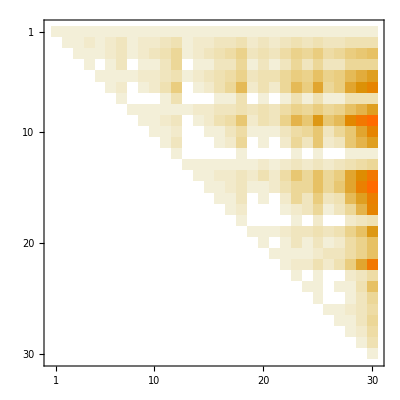

```mathematica
Table[KostkaNumber[part,part2],{part,IntegerPartitions[10,5]},{part2,IntegerPartitions[10,5]}]//MatrixPlot
```

```mathematica
Vandermonde[Table[Indexed[C,i],{i,Range[5]}]]
```

{{1,C1,C1^2,C1^3,C1^4},{1,C2,C2^2,C2^3,C2^4},{1,C3,C3^2,C3^3,C3^4},{1,C4,C4^2,C4^3,C4^4},{1,C5,C5^2,C5^3,C5^4}}

```mathematica
C/@Range[3]
```

{C[1],C[2],C[3]}